## Model and Parameters

```mathematica
Clear[Kforce,f1,f2,f1u,f2u,param,jac,CR,CRu,sol, solu]
```

```mathematica
Kforce=Amp Sin[(p 2 Pi) t + Ps*Pi];
```

```mathematica
f1=R1 r1 (1-R1/(K1+Kforce))-(a1 C1 R1/(b1+R1));

f2=C1 (e a1 R1/(b1+R1)-d1);
```

```mathematica
f1u=R1(r1(1-R1/K1)-a1 C1/(b1+R1));
f2u= C1(e a1 R1/(b1+R1)-d1);
```

```mathematica
CR[{R0_,C0_}]:=Module[{transform={R1->R1[t],C1->C1[t]}},
{R1'[t]==(f1/.transform),
C1'[t]==(f2/.transform),
R1[0]==R0,
C1[0]==C0}
]
```

```mathematica
CRu[{R0_,C0_}]:=Module[{transform={R1->R1[t],C1->C1[t]}},
{R1'[t]==(f1u/.transform),
C1'[t]==(f2u/.transform),
R1[0]==R0,
C1[0]==C0}
]
```

```mathematica
param=Dispatch[{
a1->1.3,      
r1->10.0,
K1->5.0,
d1 -> 0.20,
b1->1.,
e->0.7,
Amp->0.5,
Ps->0.0,
p -> 1
}]
```

Dispatch[…]

```mathematica
Clear[tmax]
```

```mathematica
tmax=20000
```

20000

```mathematica
sol[R0_,C0_,Kval_,rval_,eval_,freq_]:=NDSolve[CR[{R0,C0}]/.K1->Kval/.r1->rval/.e->eval/.p->freq/.param,{R1,C1},{t,0,tmax},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->100000000]
```

```mathematica
solu[R0_,C0_,Kval_,rval_,eval_]:=NDSolve[CRu[{R0,C0}]/.K1->Kval/.r1->rval/.e->eval/.param,{R1,C1},{t,0,tmax},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->100000000]
```

## Eigenvalues

### Calculate eigenvalues and Hopf solutions

From the above equations we can generate the Jacobian (use later for equilibrium calculation):

```mathematica
jac=Outer[D,{f1u,f2u},{R1,C1}];
```

```mathematica
jac//MatrixForm
```

(-(a1 C1)/(b1+R1)+r1 (1-R1/K1)+R1 (-r1/K1+(a1 C1)/(b1+R1)^2) | -(a1 R1)/(b1+R1)
C1 (-(a1 e R1)/(b1+R1)^2+(a1 e)/(b1+R1)) | -d1+(a1 e R1)/(b1+R1))

```mathematica
eqs=Solve[{f1u==0,f2u==0},{R1,C1}]
```

{{R1→0,C1→0},{R1→-(b1 d1)/(d1-a1 e),C1→-(b1 e (b1 d1+d1 K1-a1 e K1) r1)/((d1-a1 e)^2 K1)},{R1→K1,C1→0}}

```mathematica
FullSimplify[Eigenvalues[jac/.eqs[[2]]]]
```

{(a1 d1 e (-b1+K1) r1-d1^2 (b1+K1) r1+√(d1 r1 (4 a1 e (d1-a1 e)^2 K1 (b1 d1+(d1-a1 e) K1)+d1 (b1 (d1+a1 e)+(d1-a1 e) K1)^2 r1)))/(2 a1 e (-d1+a1 e) K1),-(a1 d1 e (b1-K1) r1+d1^2 (b1+K1) r1+√(d1 r1 (4 a1 e (d1-a1 e)^2 K1 (b1 d1+(d1-a1 e) K1)+d1 (b1 (d1+a1 e)+(d1-a1 e) K1)^2 r1)))/(2 a1 e (-d1+a1 e) K1)}

Take real part (remove terms under sqrt) to find equation of eigenvalue curve in destabilization phase (part under square root is negative past check mark)

```mathematica
Clear[b2]
```

```mathematica
b2 = (a1 d1 e (-b1+K1) r1-d1^2 (b1+K1) r1)/(2 a1 e (-d1+a1 e) K1);
```

b2 = 0 solves for Hopf bifurcation point above

```mathematica
Flatten[Solve[b2==0,K1]]
```

{K1→-(b1 (d1+a1 e))/(d1-a1 e)}

```mathematica
KHopf=-(b1 (d1+a1 e))/(d1-a1 e)
```

-(b1 (d1+a1 e))/(d1-a1 e)

### Integrate eigenvalues around Hopf

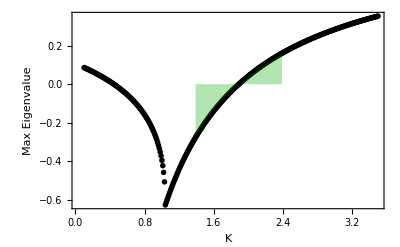

```mathematica
eigs=ParallelTable[{val,Max[Re[Eigenvalues[jac/.eqs[[2]]/.K1->val/.r1->5/.e->0.5/.param]]]},{val,0.1,3.5,0.01}];

Keigs[rval_,eval_]:=ParallelTable[{Kval,Max[Re[Eigenvalues[jac/.eqs[[2]]/.K1->Kval/.r1->rval/.e->eval/.param]]]},{Kval,KHopf-Amp/.e->eval/.param,KHopf+Amp/.e->eval/.param,0.01}]

Show[{
ListPlot[eigs,Frame->True,Axes->True,PlotStyle->Directive[Black,PointSize[0.01]],FrameLabel->{"K","Max Eigenvalue"},PlotRange->{All,All}],
ListLinePlot[Keigs[5,0.5],Filling->Axis,PlotStyle->Black,FillingStyle->Directive[Darker[Green],Opacity[0.3]], Frame->False,Axes->False]}]
```

#### Plot integrals across Kmean and different r (Figure 3)

```mathematica
Keigdiff[rval_,eval_]:=ParallelTable[{Kmean,Sum[Max[Re[Eigenvalues[jac/.eqs[[2]]/.K1->Kval/.r1->rval/.e->eval/.param]]]-Max[Re[Eigenvalues[jac/.eqs[[2]]/.K1->Kmean/.r1->rval/.e->eval/.param]]],{Kval,Kmean-Amp/.r1->rval/.e->eval/.param,Kmean+Amp/.r1->rval/.e->eval/.param,0.01}]},
{Kmean, KHopf/.r1->rval/.e->eval/.param,KHopf+2 Amp /.r1->rval/.e->eval/.param, 0.05}]
```

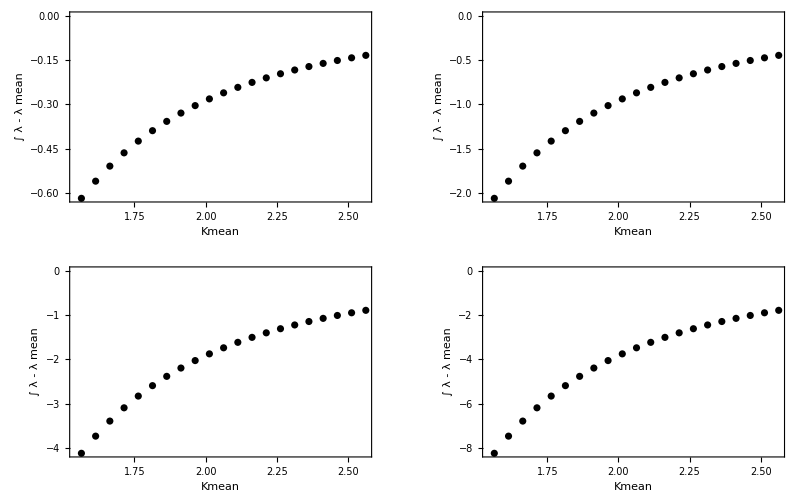

```mathematica
GraphicsGrid[{
{ListPlot[Keigdiff[1.5,0.7],PlotStyle->Black, Frame->True,Axes->True,FrameLabel->{"Kmean","∫ λ - λ mean"}],
ListPlot[Keigdiff[5,0.7],PlotStyle->Black, Frame->True,Axes->True,FrameLabel->{"Kmean","∫ λ - λ mean"}]},
{ListPlot[Keigdiff[10,0.7],PlotStyle->Black, Frame->True,Axes->True,FrameLabel->{"Kmean","∫ λ - λ mean"}],
ListPlot[Keigdiff[20,0.7],PlotStyle->Black, Frame->True,Axes->True,FrameLabel->{"Kmean","∫ λ - λ mean"}]}
}]
```

## Forcing speed x CV (Figure 2)

#### First do CV of C densities

```mathematica
pvals=Table[10^i,{i,-3,1,0.01}];
```

```mathematica
CVforce[Kval_, rval_,eval_]:=ParallelTable[{freq,StandardDeviation[Flatten[Evaluate[C1[Range[tmax-Max[4/freq,1000],tmax]]/.sol[0.5,0.5,Kval,rval,eval,freq]]]]/Mean[Flatten[Evaluate[C1[Range[tmax-Max[4/freq,1000],tmax]]/.sol[0.5,0.5,Kval,rval,eval,freq]]]]},{freq,pvals}];
```

```mathematica
CVur[Kval_,eval_]:=ParallelTable[{rval,StandardDeviation[Flatten[Evaluate[C1[Range[9900,10800]]/.solu[0.5,0.5,Kval,rval,eval]]]]/Mean[Flatten[Evaluate[C1[Range[9900,10800]]/.solu[0.5,0.5,Kval,rval,eval]]]]},{rval,{1.5,5,10,20}}];
```

```mathematica
CVur[KHopf+0.05,0.7]
```

{{1.5,0.149948},{5,0.0824255},{10,0.0586026},{20,0.0419397}}

```mathematica
CVur[KHopf+0.2,0.7]
```

{{1.5,0.29727},{5,0.165829},{10,0.120143},{20,0.0893137}}

#### Make separate dataframes (outside plots) of all parameters so we can save them and make plotting easier later on

```mathematica
cvlowrk005=CVforce[KHopf+0.05/.param,1.5,0.7];
```

```mathematica
cvmedlowrk005=CVforce[KHopf+0.05/.param,5,0.7];
```

```mathematica
cvmedhirk005=CVforce[KHopf+0.05/.param,10,0.7];
```

```mathematica
cvhirk005=CVforce[KHopf+0.05/.param,20,0.7];
```

```mathematica
STNDcvlowrk005 = Table[{cvlowrk005[[i,1]],cvlowrk005[[i,2]]-0.14994835360468475},{i,1,Length[cvlowrk005]}];
```

```mathematica
STNDcvmedlowrk005 = Table[{cvmedlowrk005[[i,1]],cvmedlowrk005[[i,2]]-0.08242551568723415},{i,1,Length[cvmedlowrk005]}];
```

```mathematica
STNDcvmedhirk005 = Table[{cvmedhirk005[[i,1]],cvmedhirk005[[i,2]]-0.05860260567066161},{i,1,Length[cvmedhirk005]}];
```

```mathematica
STNDcvhirk005 = Table[{cvhirk005[[i,1]],cvhirk005[[i,2]]-0.04193970934702077},{i,1,Length[cvhirk005]}];
```

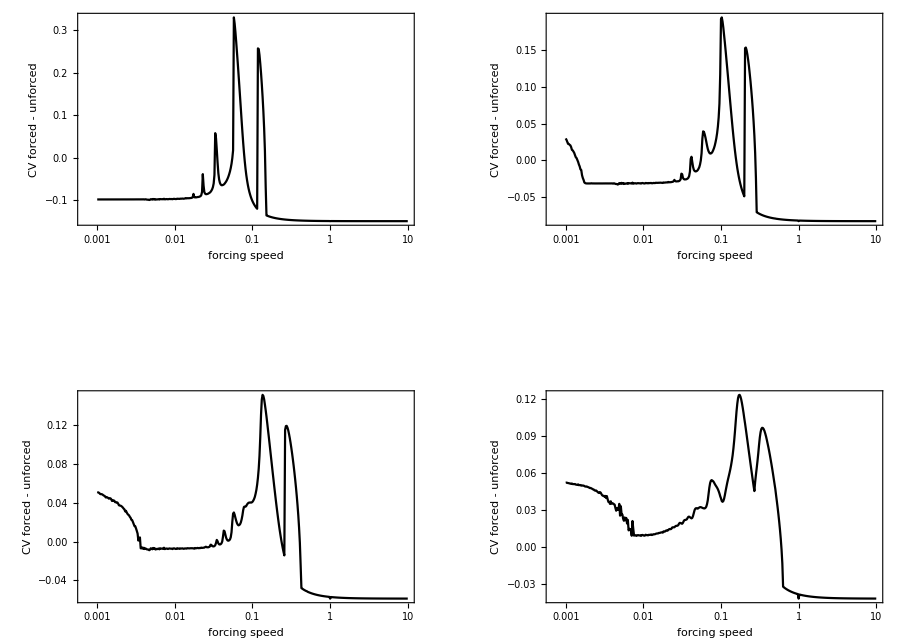

```mathematica
GraphicsGrid[{
{ListLinePlot[{STNDcvlowrk005}, Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.008]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350],
ListLinePlot[{STNDcvmedlowrk005},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.008]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350]},
{ListLinePlot[{STNDcvmedhirk005},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.008]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350],
ListLinePlot[{STNDcvhirk005},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.008]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350]}
},ImageSize->900,Spacings->{30,90}]
```

### Repeat Fig 2 in main text for different mean K and e values) (Appendix Figure A1 & A2)

```mathematica
lesspvals=Table[10^i,{i,-3,1,0.05}];
```

```mathematica
CVforcesupp[Kval_, rval_,eval_]:=ParallelTable[{freq,StandardDeviation[Flatten[Evaluate[C1[Range[tmax-Max[4/freq,1000],tmax]]/.sol[0.5,0.5,Kval,rval,eval,freq]]]]/Mean[Flatten[Evaluate[C1[Range[tmax-Max[4/freq,1000],tmax]]/.sol[0.5,0.5,Kval,rval,eval,freq]]]]},{freq,lesspvals}];
```

```mathematica
CVuK[rval_,eval_]:=ParallelTable[{StandardDeviation[Flatten[Evaluate[C1[Range[9900,10800]]/.solu[0.5,0.5,Kval,rval,eval]]]]/Mean[Flatten[Evaluate[C1[Range[9900,10800]]/.solu[0.5,0.5,Kval,rval,eval]]]]},{Kval,{KHopf-Amp,KHopf-0.25,KHopf+0.25,KHopf+Amp}}];
```

```mathematica
CVuK[10,0.7]
```

{{0.},{0.},{0.13551},{0.198431}}

```mathematica
cvlowk=CVforcesupp[KHopf-Amp/.param,1.5,0.7];
```

```mathematica
cvmedlowk=CVforcesupp[KHopf-0.25/.param,5,0.7];
```

```mathematica
cvmedhik=CVforcesupp[KHopf+0.25/.param,10,0.7];
```

```mathematica
cvhik=CVforcesupp[KHopf+Amp/.param,20,0.7];
```

```mathematica
STNDcvlowk = Table[{cvlowk[[i,1]],cvlowk[[i,2]]-0},{i,1,Length[cvlowk]}];
```

```mathematica
STNDcvmedlowk = Table[{cvmedlowk[[i,1]],cvmedlowk[[i,2]]-0},{i,1,Length[cvmedlowk]}];
```

```mathematica
STNDcvmedhik = Table[{cvmedhik[[i,1]],cvmedhik[[i,2]]-0.135510013},{i,1,Length[cvmedhik]}];
```

```mathematica
STNDcvhik = Table[{cvhik[[i,1]],cvhik[[i,2]]-0.198431388},{i,1,Length[cvhik]}];
```

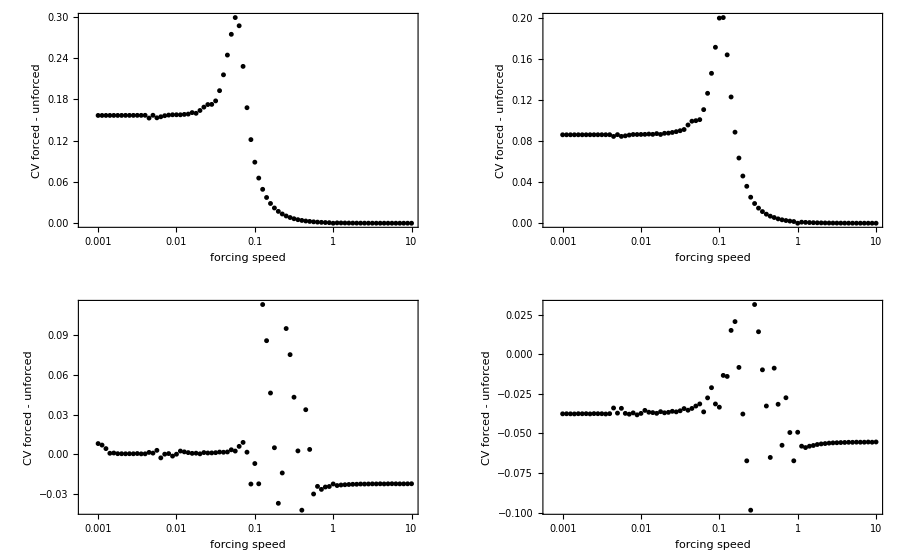

```mathematica
GraphicsGrid[{
{ListPlot[{STNDcvlowk}, Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350],
ListPlot[{STNDcvmedlowk},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350]},
{ListPlot[{STNDcvmedhik},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350],
ListPlot[{STNDcvhik},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350]}
},ImageSize->900]
```

```mathematica
cvlowek005=CVforcesupp[KHopf+0.05/.e->0.3/.param,10,0.3];
```

```mathematica
cvmedlowek005=CVforcesupp[KHopf+0.05/.e->0.5/.param,10,0.5];
```

```mathematica
cvhiek005=CVforcesupp[KHopf+0.05/.e->0.95/.param,10,0.95];
```

```mathematica
STNDcvlowek005 = Table[{cvlowek005[[i,1]],cvlowek005[[i,2]]-0.03053674711638994},{i,1,Length[cvlowek005]}];
```

```mathematica
STNDcvmedlowek005 = Table[{cvmedlowek005[[i,1]],cvmedlowek005[[i,2]]-0.04643701941803326},{i,1,Length[cvmedlowek005]}];
```

```mathematica
STNDcvhiek005 = Table[{cvhiek005[[i,1]],cvhiek005[[i,2]]-0.07104389349180776},{i,1,Length[cvhiek005]}];
```

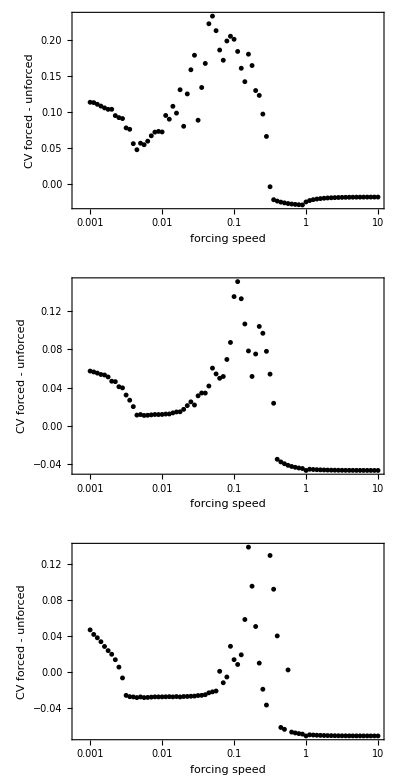

```mathematica
GraphicsColumn[{
ListPlot[{STNDcvlowek005}, Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350],
ListPlot[{STNDcvmedlowek005},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350],
ListPlot[{STNDcvhiek005},Frame->True,ScalingFunctions->{"Log"},
Axes->True,PlotStyle->{Directive[Black,PointSize[0.01]]},PlotRange->{All,All},
FrameLabel->{"forcing speed","CV forced - unforced"},ImageSize->350]
},ImageSize->400]
```

## Time series and phaseplane trajectories

### Phaseplane trajectories vs max and min attractors, isoclines - use manipulate to adjust parameters

```mathematica
Manipulate[Show[Plot[{-(r1 (b1+R) (-K1+R))/(a1 K1)/.K1->(KHopf+Kadd/.e->eval/.param)/.r1->rval/.param},  {R, 0, 2},PlotRange->{{0,1.5},{5,12.0}},FrameLabel->{Style["Resource",FontSize->14,Bold],Style["Consumer",FontSize->14,Bold]},Frame->True, Axes -> True,PlotStyle->{Gray,Thickness[.005]},AspectRatio->1.3],
Plot[{-(r1 (b1+R) (-K1+R))/(a1 K1)/.K1->(KHopf+Kadd+Amp/.Amp->Kamp/.e->eval/.param)/.r1->rval/.param},  {R, 0, 2},PlotStyle->{Gray,Thickness[.003],Dashed}],
Plot[{-(r1 (b1+R) (-K1+R))/(a1 K1)/.K1->(KHopf+Kadd-Amp/.Amp->Kamp/.e->eval/.param)/.r1->rval/.param},  {R, 0, 2},PlotStyle->{Gray,Thickness[.003],Dashed}],Graphics[{Thickness[0.005],Lighter[Gray],Line[{{(d1 b1/(a1 e - d1))/.e->eval/.param,0},{(d1 b1/(a1 e - d1))/.e->eval/.param,20}}]}],

ParametricPlot[Evaluate[{R1[t],C1[t]}/.sol[R0,C0,KHopf+Kadd/.e->eval,rval,eval,pval]],{t,tmax-2/pval,tmax},Frame->True,FrameLabel->{"R","C"},PlotLegends->{"forced trajectory"},PlotStyle->Black],ParametricPlot[Evaluate[{R1[t],C1[t]}/.solu[R0,C0,KHopf+Kadd+Amp/.Amp->Kamp/.e->eval,rval,eval]],{t,900,1000},Frame->True,FrameLabel->{"R","C"},PlotStyle->{LightPurple,Thickness[.003]},PlotLegends->{"Kmax attractor"}],
ParametricPlot[Evaluate[{R1[t],C1[t]}/.solu[R0,C0,KHopf+Kadd-Amp/.Amp->Kamp/.e->eval,rval,eval]],{t,900,1000},Frame->True,FrameLabel->{"R","C"},PlotStyle->{Darker[LightGreen],Thickness[.003]},PlotLegends->{"Kmin attractor"}],
ParametricPlot[Evaluate[{R1[t],C1[t]}/.solu[R0,C0,KHopf+Kadd/.e->eval,rval,eval]],{t,900,1000},Frame->True,FrameLabel->{"R","C"},PlotStyle->{LightOrange,Thickness[.005]},PlotLegends->{"Kmean attractor"}],
ImageSize->400],
{{R0,0.5},0.1,10,0.1,Appearance->"Labeled"},
{{C0,0.5},0.1,10,0.1,Appearance->"Labeled"},
{{pval,0.01},0.001,5,0.005,Appearance->"Labeled"},
{{eval,0.7},0.01,1,0.01,Appearance->"Labeled"},
{{rval,10.0},0.1,20,0.5,Appearance->"Labeled"},
{{Kadd,0.05},-0.5,1.0,0.1,Appearance->"Labeled"},
{{Kamp,0.5},0.0,1.0,0.1,Appearance->"Labeled"}]
```

### Time Series (Figure 4)

#### A) p = 0.5

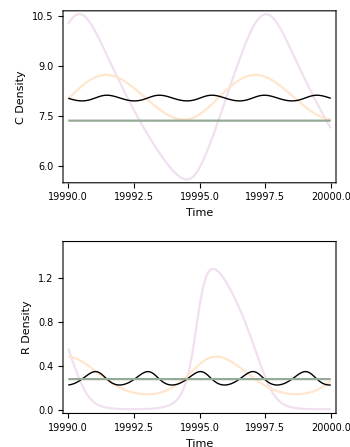

```mathematica
GraphicsColumn[{Show[Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05, 10,0.7]],{t,19990,20000},PlotStyle->LightPurple,
Frame->True,FrameLabel->{"Time","C Density"},PlotRange->{All,All},ImageSize->350],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+0.05, 10,0.7]],{t,19990,20000},PlotStyle->LightOrange],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05, 10,0.7]],{t,19990,20000},PlotStyle->Darker[LightGreen]],
Plot[Evaluate[{C1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.5]],{t,19990,20000},
PlotStyle->Directive[Black,Thick]]],
Show[Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05,10,0.7]],{t,19990,20000},PlotStyle->LightPurple,Frame->True,PlotRange->{All,{0,1.5}},FrameLabel->{"Time","R Density"},ImageSize->350],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+0.05,10,0.7]],{t,19990,20000},PlotStyle->LightOrange],
Plot[Evaluate[{R1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.5]],{t,19990,20000},PlotStyle->Directive[Black,Thick],PlotRange->{All,All}],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05,10,0.7]],{t,19990,20000},PlotStyle->Darker[LightGreen]]]},ImageSize->350]
```

#### B) p = 0.05

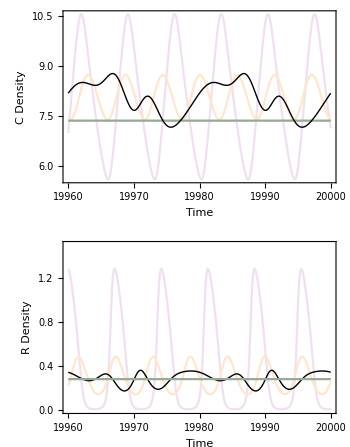

```mathematica
GraphicsColumn[{Show[Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05, 10,0.7]],{t,19960,20000},PlotStyle->LightPurple,
Frame->True,FrameLabel->{"Time","C Density"},PlotRange->{All,All},ImageSize->350],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+0.05, 10,0.7]],{t,19960,20000},PlotStyle->LightOrange],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05, 10,0.7]],{t,19960,20000},PlotStyle->Darker[LightGreen]],
Plot[Evaluate[{C1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.05]],{t,19960,20000},
PlotStyle->Directive[Black,Thick]]],
Show[Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05,10,0.7]],{t,19960,20000},PlotStyle->LightPurple,Frame->True,PlotRange->{All,{0,1.5}},FrameLabel->{"Time","R Density"},ImageSize->350],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+0.05,10,0.7]],{t,19960,20000},PlotStyle->LightOrange],
Plot[Evaluate[{R1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.05]],{t,19960,20000},PlotStyle->Directive[Black,Thick],PlotRange->{All,All}],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05,10,0.7]],{t,19960,20000},PlotStyle->Darker[LightGreen]]]},ImageSize->350]
```

#### C) p = 0.01

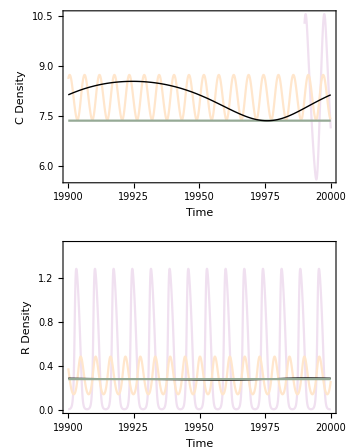

```mathematica
GraphicsColumn[{Show[Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05, 10,0.7]],{t,19990,20000},PlotStyle->LightPurple,
Frame->True,FrameLabel->{"Time","C Density"},PlotRange->{All,All},ImageSize->350],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+0.05, 10,0.7]],{t,19900,20000},PlotStyle->LightOrange],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05, 10,0.7]],{t,19900,20000},PlotStyle->Darker[LightGreen]],
Plot[Evaluate[{C1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.01]],{t,19900,20000},
PlotStyle->Directive[Black,Thick]]],
Show[Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05,10,0.7]],{t,19900,20000},PlotStyle->LightPurple,Frame->True,PlotRange->{All,{0,1.5}},FrameLabel->{"Time","R Density"},ImageSize->350],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+0.05,10,0.7]],{t,19900,20000},PlotStyle->LightOrange],
Plot[Evaluate[{R1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.01]],{t,19900,20000},PlotStyle->Directive[Black,Thick],PlotRange->{All,All}],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05,10,0.7]],{t,19900,20000},PlotStyle->Darker[LightGreen]]]},ImageSize->350]
```

#### D) p = 0.001

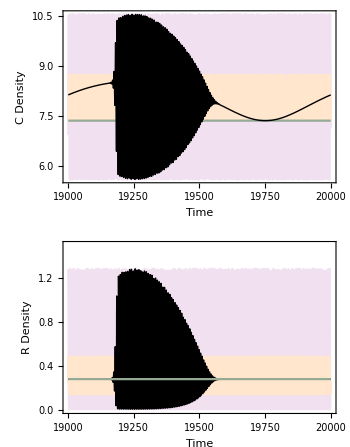

```mathematica
GraphicsColumn[{Show[Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05, 10,0.7]],{t,19000,20000},PlotStyle->LightPurple,
Frame->True,FrameLabel->{"Time","C Density"},PlotRange->{All,All},ImageSize->350],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf+0.05, 10,0.7]],{t,19000,20000},PlotStyle->LightOrange],
Plot[Evaluate[{C1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05, 10,0.7]],{t,19000,20000},PlotStyle->Darker[LightGreen]],
Plot[Evaluate[{C1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.001]],{t,19000,20000},
PlotStyle->Directive[Black,Thick]]],
Show[Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+Amp+0.05,10,0.7]],{t,19000,20000},PlotStyle->LightPurple,Frame->True,PlotRange->{All,{0,1.5}},FrameLabel->{"Time","R Density"},ImageSize->350],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf+0.05,10,0.7]],{t,19000,20000},PlotStyle->LightOrange],
Plot[Evaluate[{R1[t]}/.sol[0.5,0.5,KHopf+0.05,10,0.7,0.001]],{t,19000,20000},PlotStyle->Directive[Black,Thick],PlotRange->{All,All}],
Plot[Evaluate[{R1[t]}/.solu[0.5,0.5,KHopf- Amp +0.05,10,0.7]],{t,19000,20000},PlotStyle->Darker[LightGreen]]]},ImageSize->350]
```

## Bifurcation diagrams for C and R (local max & min across forcing speed, p)

```mathematica
pBif2[freq_]:=Module[{sol,solTrans,tstart,width,tend=14000,i0,crit,points},
width=Max[4/freq,1000];
tstart=tend-width;
solTrans=First@NDSolve[CR[{0.3,8.5}]/.K1->KHopf+0.05/.p->freq/.param,{R1,C1},{t,0,tstart},MaxStepSize->0.01,MaxSteps->∞,Method->"StiffnessSwitching"];
i0={R1[tstart],C1[tstart]}/.solTrans;
crit=WhenEvent[C1'[t]==0&&t>500,Sow[C1[t]]];
{sol,points}=Reap@NDSolve[{CR[i0]/.K1->KHopf+0.05/.p->freq/.param,crit},{R1,C1},{t,0,width},MaxStepSize->0.01,MaxSteps->∞,Method->"StiffnessSwitching"];
If[Length[points]==0,
{{freq,First[C1[width]/.sol]}}, 
Thread[{freq,First[points]}]
]
]
```

```mathematica
pBifR[K1in_,rval_,eval_,freq_]:=Module[{sol,solTrans,tstart,width,tend=14000,i0,crit,points},
width=Max[4/freq,1000];
tstart=tend-width;
solTrans=First@NDSolve[CR[{0.5,0.5}]/.K1->K1in/.r1->rval/.e->eval/.p->freq/.param,{R1,C1},{t,0,tstart},MaxStepSize->0.01,MaxSteps->∞];
i0={R1[tstart],C1[tstart]}/.solTrans;
crit=WhenEvent[R1'[t]==0&&t>500,Sow[R1[t]]];
{sol,points}=Reap@NDSolve[{CR[i0]/.K1->K1in/.r1->rval/.e->eval/.p->freq/.param,crit},{R1,C1},{t,0,width},MaxStepSize->0.01,MaxSteps->∞];
If[Length[points]==0,
{{freq,First[R1[width]/.sol]}}, 
Thread[{freq,First[points]}]
]
]
```

```mathematica
pbifvals=Table[10^i,{i,-3,0.2,0.01}];
```

```mathematica
pbif2=Flatten[ParallelTable[{pBif2[pval]},{pval,pbifvals}],1];
```

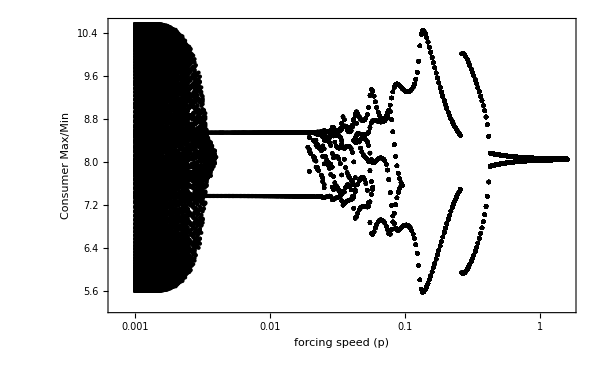

```mathematica
ListPlot[
pbif2,
Frame->True,Axes->True,ScalingFunctions->{"Log"},
PlotStyle->{Directive[Black,PointSize[0.005]]},
FrameLabel->{"forcing speed (p)","Consumer Max/Min"},PlotRange->{All,All},ImageSize->600]
```

```mathematica
pbifR=Flatten[ParallelTable[{pBifR[KHopf+0.05,10,0.7,pval]},{pval,pbifvals}],1];
```

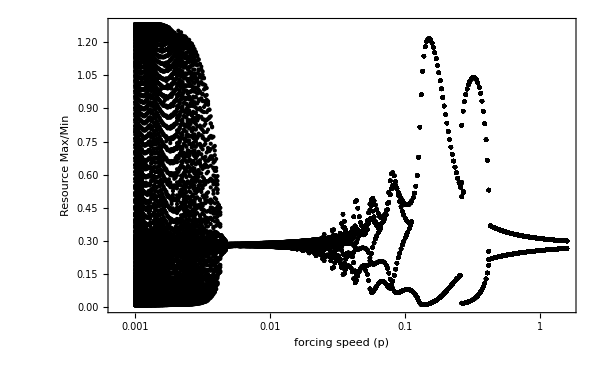

```mathematica
ListPlot[
pbifR,
Frame->True,Axes->True,
PlotStyle->{Directive[Black,PointSize[0.005]]},ScalingFunctions->{"Log"},
FrameLabel->{"forcing speed (p)","Resource Max/Min"},PlotRange->{All,All},ImageSize->600]
```